## MICA: Measurement, Instrumentation, Control & Analysis

## Force and Temperature Sensor Demo

#### Ariel Mobius, 27 February 2026

```mathematica
-Graphics--Graphics-
```

#### Revisions

2025		Feb 	18	Started
			19	Added inter-sample interval analysis and method to determine ADC resolution from noise signals	
			20	Added force probability distribution function and detrending
2026		Feb	16	Updated
			17	Added photo of setup and added Experiment 2

#### Objectives

To measure force and temperature sensor fluctuations (noise levels). After calibration using a 1 kg mass, the force fluctuations occurring with no load are measured using a full bridge strain gage force sensor (often called a load cell) connected to a TinkerForge Load Cell Bricklet. The temperature is measured using a Type K thermocouple connected to a TinkerForge Thermocouple Bricklet. The force and temperature are both sampled at 50 Hz until 10,000 samples have been acquired. The resulting force and temperature signal amplitudes (but not frequencies) are then analyzed using a variety of signal processing techniques. Analysis of the sequential structure of the signals (i.e., via power spectra or auto-correlation functions) will be covered in subsequent notes.

#### Keywords

Force,  Strain Gage, Force Sensor, Full Bridge Strain Gage,  Analog to Digital Convertor (ADC), Dynamic Range, 24 bit ADC, Sampling Rate, Sampling Jitter, Sampling Increment,  Inter-Sample Interval (ISI), Dynamic Range, Thermocouple, Type K Thermocouple, Type J Thermocouple, Histogram, Parametric Probability Density Function, Non-parametric Probability Density Function, Parametric Probability Distribution Function, Non-parametric Probability Distribution Function,  Gaussian Noise, Gaussian Probability Density, Uniform Probability Density, Drift, Detrending, Linear Trend, Differencing

#### Notes

Code that must be evaluated for the subsequent code to run properly starts with a black square (■). You click on this square to evaluate the adjacent code. All other code may be optionally evaluated in the usual way (Shift Enter or on a numerical key pad: Enter).

#### CAD Model

The OnShape CAD model can be found here: https://cad.onshape.com/documents/5af8e4ac9f87a7429a9a9a18/w/89f71a08201f28d04642e442/e/b4b22e636d3e82dade508473?renderMode=0&uiState=6993c667ba0abf89426302a6

#### Calibrate Force Sensor (Load Cell)

Use the TinkerForge Viewer to calibrate the force sensor. The calibrated value will be saved in the bricklet for subsequent use.
Select the “Calibration” button and press “Calibrate Zero” with nothing touching the force sensor. Now put a 1 kg mass on the sensor and enter 10,000,000 (as 10000000) and press “Calibrate Weight”. The reason we use 10,000,000 rather than 1,000 is because we wish to have the force sensor make measurements in 0.1 milligram force increments rather than grams. We just have to remember this when we subsequently convert force sensor measurements to Newtons (N).

#### Thermocouple

The TinkerForge Thermocouple Bricklet supports all the main thermocouple types:  B, E, J, K, N, R, S and T . The most frequently used thermocouples are the Type K and J. Thermocouples are made by welding two different alloys together to form a bead. The ones used in class are type K and have a bead diameter of about 1 mm. Thermocouples are available with bead diameters of 100 μm (fairly common) and less. The smaller the bead diameter the faster the response to changing temperature. The mV level voltage generated by the welded alloys is converted to a temperature in digital form within the TinkerForge Thermocouple Bricklet. Each thermocouple type has a different nonlinear voltage to temperature relation which is usually represented as a high order polynomial. The Bricklet also determines which thermocouple is inserted in to it and invokes the appropriate voltage to temperature polynomial. 
It is important to note that Thermocouples should not be considered as precision measurement devices and rarely do better than ±1 ∘C without calibration. Consider using a platinum resistive temperature sensor for more accurate temperature measurements.
A typical thermocouple connector is polarized. The +ve part of the connector is 2.5 mm wide and the other is 3 mm wide. Be aware of this when inserting.

#### Connect to TinkerForge

In order to communicate with the TinkerForge Bricks and Bricklets from Mathematica you need to add the TinkerForge.dll file to your system.
To do this, if you have not already done so you need to go to:
 https://www.tinkerforge.com/en/doc/Software/API_Bindings_Mathematica.html#api-bindings-mathematica
 and click on the ZIP file link.
 Download it and open it and Copy the TinkerForge.dll file.
 Then go to your Wolfram directory and navigate to the NETLink subdirectory. On the Mac it is at:
 /Applications/Wolfram.app/Contents/SystemFiles/Links/NETLink
and Paste the TinkerForge.dll file.
You will need to restart Mathematica.

```mathematica
"■";  (* Windows Only *)
Needs["NETLink`"];
LoadNETAssembly["Tinkerforge"];
```

```mathematica
"■";  (* Mac Only *)
(* for both Linux and Max OS need to load Mono from https://www.mono-project.com/download/stable/ *)
Needs["NETLink`"];
InstallNET["MonoPath"->"/Library/Frameworks/Mono.framework/Versions/Current/Commands/mono"];
LoadNETAssembly["Tinkerforge",NotebookDirectory[]];
```

```mathematica
"■";  host="localhost";
port=4223;
ipcon=NETNew["Tinkerforge.IPConnection"];
(* as usual you need to use the Brick Viewer to find the unique identifiers (UID) for each bricklet and insert below *)
tc=NETNew["Tinkerforge.BrickletThermocoupleV2","LBv",ipcon];
lc=NETNew["Tinkerforge.BrickletLoadCellV2","1b4s",ipcon];
ipcon@Connect[host,port];
```

#### Setup TinkerForge Load Cell Bricklet

By default the Load Cell Bricklet takes the average of every 4 samples with a moving average filter. We do not want such averaging so we need to turn it off by setting the average to 1 (i.e. no averaging):

```mathematica
"■";  lc@SetMovingAverage[1];
```

By default the Load Cell Bricklet samples at 10 Hz but can sample at 80 Hz which is what we want. It also has 3 gain settings (32x, 64x, and 128x). We want 128x. Lets set these:

```mathematica
"■";  lc@SetConfiguration[BrickletLoadCellV2`RATEU80HZ,BrickletLoadCellV2`GAINU128X];
```

#### Setup TinkerForge Thermocouple Bricklet

By default the Thermocouple Bricklet averages ever 16 samples. We do not want this so we need to explicitly set this to 1.
The Thermocouple Bricklet can infer the thermocouple type, but as we know that it is Type K  we will specify this.
Thermocouples tend to pick up voltages induced by adjacent equipment connected to the mains (wall outlet) power which in the US is 120 V, 60 Hz).
The Thermocouple Bricklet includes a digital filter designed to attenuate this induced “noise”. The default is 50 Hz but as we are in the US we will set it to 60 Hz.

```mathematica
"■";  tc@SetConfiguration[BrickletThermocoupleV2`AVERAGINGU1,BrickletThermocoupleV2`TYPEUK,BrickletThermocoupleV2`FILTERUOPTIONU60HZ];
```

#### Check Force Sensor

```mathematica
"■";  9.81 (lc@GetWeight[])/10000000(* convert to N *)
```

9.86227

#### Check Thermocouple Temperature Sensor

```mathematica
"■";  tc@GetTemperature[]/100.0
```

22.36

#### Polling Code

We could use Pause[] to specify the time between samples in a loop but this is not accurate and always results in times between samples  that are larger than the Pause[] time. A better approach is  to use a method called polling where we wait for a specified time as specified by a computer absolute timer and then take a measurement. Lets  look at how this works when we desire an increment of 1 s

```mathematica
"■"; δt=1.0; (* desired inter-sample interval in s *)
t0=AbsoluteTime[];
While[(AbsoluteTime[]-t0)< δt];
AbsoluteTime[]-t0
```

1.009158

Try running this a few times.

This approach allows us to do many things between successive samples. In the following code we record how many times the While[] function is evaluated, n, while its waits for the AbsoluteTime to advance by 1 s:

```mathematica
"■"; δt=1.0; (* desired inter-sample interval in s *)
n=0;
a=1.0;
t0=AbsoluteTime[];
While[(AbsoluteTime[]-t0)< δt,n=n+1;a=a*1.0001-0.00001];
{3 n,AbsoluteTime[]-t0}
```

{599718,1.00701}

Here we can see that in the time interval (1 s in this case) we did around 3 n = 1.5 million (it will be different on different computers, the higher the number the faster your computer) floating point operations (addition, multiplication and subtraction) while we waited for the AbsoluteTime to advance by 1 s.

#### Experiment 1: Measure Force (with no load) and Temperature for 200 s

We set TinkerForge Load Cell Bricklet to have an internal sampling rate of 80 Hz. To avoid the possibility of reading the same sample more than once we need to read the Load Cell Bricklet at less than this value. So in the following experiment we will sample it and the thermocouple at 50 Hz (i.e., once every 20 ms). We will collect 10,000 samples per signal. 10,000 samples x 0.02 s = 200 s experimental duration. We will use polling as outlined above. You should avoid bumping the setup while running the experiment:

```mathematica
"■"; 
n=10000;
time1=Table[0,n];
temperature1=Table[0,n]; (* in oC *)
force1=Table[0,n]; (* in Newtons *)
δt=0.02; (* desired inter-sample interval in s *)
t0=AbsoluteTime[];
Do[
While[(AbsoluteTime[]-t0)< δt(i-1)];
time1[[i]]= AbsoluteTime[]-t0; 
temperature1[[i]]=tc@GetTemperature[]/100.0;
force1[[i]]=9.81 (lc@GetWeight[])/10000000;
If[Mod[i,1000]==0, (* print out every 1000th sample index *)
Print[i]],
{i,n}]
```

1000

2000

3000

4000

5000

6000

7000

8000

9000

10000

#### Store Data

By default Mathematica does not store large amounts of data. We can force it store our force and temperature signals using:

```mathematica
"■";  PersistentSymbol["NoLoadForceTemperatureData"]={time1,force1,temperature1};
```

#### Quick Plots

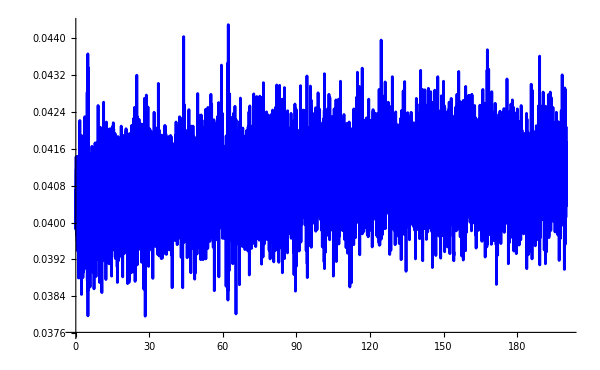

```mathematica
"■"; ListLinePlot[{time1,force1}ᵀ,PlotRange->All,PlotStyle->Blue,ImageSize->600]
```

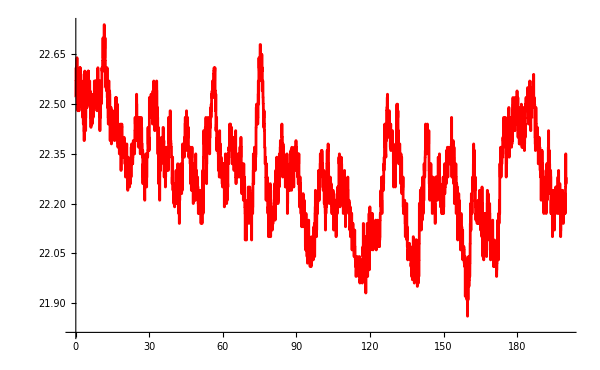

```mathematica
"■"; ListLinePlot[{time1,temperature1}ᵀ,PlotRange->All,PlotStyle->Red,ImageSize->600]
```

Clearly these two signals look very different.

#### Analyze Sample Times

The first thing we want to do is to check that our sampling rate was fairly constant at 50 Hz. Here are the first two inter-sample intervals (ISI):

```mathematica
"■";  time1[[2]]-time1[[1]]
```

0.028945

```mathematica
"■";  time1[[3]]-time1[[2]]
```

0.018919

Lets find all the n-1 inter-sample intervals. We use the function Differences[] for this:

```mathematica
"■";  timeInc=Differences[time1];
```

Lets plot these  inter-sample intervals:

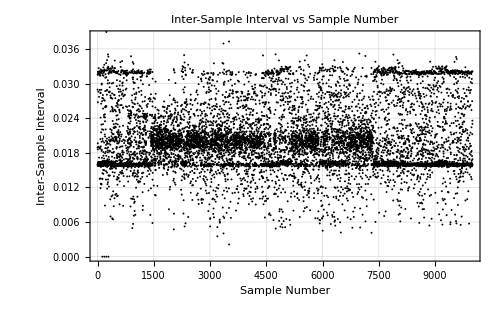

```mathematica
"■";  ListPlot[timeInc,PlotStyle->Black,PlotTheme->"Detailed",FrameLabel->{"Sample Number","Inter-Sample Interval"},LabelStyle->{12,Black},PlotLabel->"Inter-Sample Interval vs Sample Number",ImageSize->500]
```

It looks as though most of the  inter-sample intervals are at the desired 0.02 s with some a little less and some a little more. The deviations from the desired  inter-sample interval are called “sampling jitter”.
Lets look at the worst case minimum and maximum  inter-sample intervals:

```mathematica
"■";  {Min[timeInc],Max[timeInc]}
```

{0.,0.050239}

The standard deviation of the jitter is:

```mathematica
"■";  StandardDeviation[timeInc]
```

0.005494

As a percentage of the desired  inter-sample interval the sampling jitter is:

```mathematica
"■";  100 StandardDeviation[timeInc]/0.02
```

27.4716

This is clearly not zero but if the sampling jitter is less than 1 % then it is probably acceptable.

#### Inter-Sample Interval Probability Density Function

Lets determine the histogram of the inter-sample intervals:

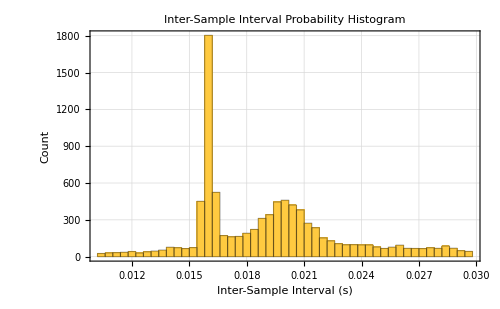

```mathematica
"■";  Histogram[timeInc,{0.0102,0.03,0.0004},"Count",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Inter-Sample Interval (s)","Count"},LabelStyle->{12,Black},PlotLabel->"Inter-Sample Interval Probability Histogram",ImageSize->500]
```

Here we selected a bin width of 0.0004 s.

Histogram values change when we change the number of samples and/or the bin width. We need a way to normalize the histogram so that we can compare results across different experiments (with different sample sizes and bin widths) and to compare with theory. The probability density function gives us this. You can determine the probability density function from the histogram by dividing by the sample size (converts to a probability function) and then by the bin width (coverts to a probability density). The result is a normalized function where the area under it is always = 1. Lets plot the probability density of the inter-sample intervals:

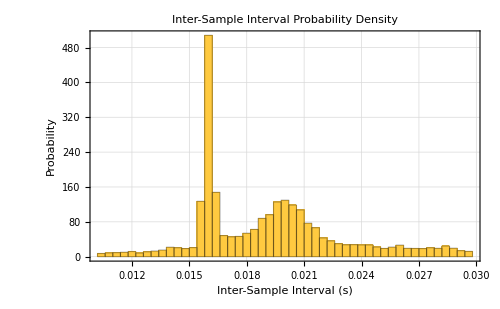

```mathematica
"■";  Histogram[timeInc,{0.0102,0.03,0.0004},"PDF",PlotTheme->"Detailed",FrameLabel->{"Inter-Sample Interval (s)","Probability"},LabelStyle->{12,Black},PlotLabel->"Inter-Sample Interval Probability Density",ImageSize->500]
```

Note that the area under this probability density function is 1.
We can determine the integral of the probability density which is called the probability distribution function (or the cumulative density function):

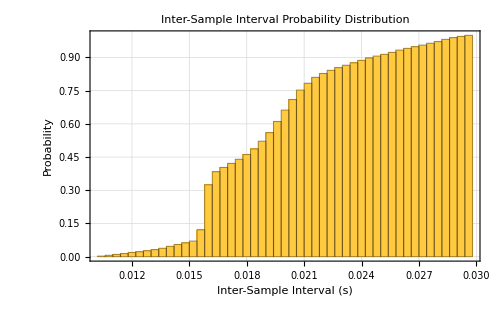

```mathematica
"■";  Histogram[timeInc,{0.0102,0.03,0.0004},"CDF",PlotTheme->"Detailed",FrameLabel->{"Inter-Sample Interval (s)","Probability"},LabelStyle->{12,Black},PlotLabel->"Inter-Sample Interval Probability Distribution",ImageSize->500]
```

Sometimes it is helpful to plot the histogram counts at each inter-sample interval on a log axis:

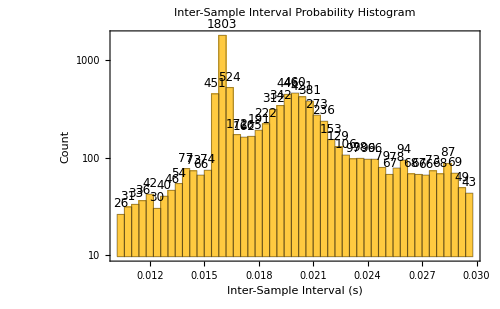

```mathematica
"■";  Histogram[timeInc,{0.0102,0.03,0.0004},"LogCount",LabelingFunction->Above,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Inter-Sample Interval (s)","Count"},LabelStyle->{12,Black},PlotLabel->"Inter-Sample Interval Probability Histogram",ImageSize->500]
```

Now we can see that the inter-sample intervals that were significantly different from the desired value of 0.02 s, only occurred a few times.

It is clear that most of the inter-sample increments are at or close to the desired 0.02 s.

Probability density functions determined from data such as those above are termed non-parametric probability density functions to distinguish them from the parametric probability density functions such as Gaussian probability density functions which are specified by an equation.

#### Force Signal Amplitude Analysis

Lets plot the force signal again:

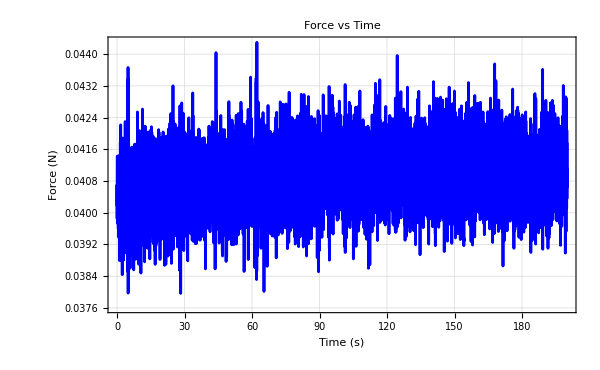

```mathematica
"■"; ListLinePlot[{time1,force1}ᵀ,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Force (N)"},LabelStyle->{12,Black},PlotLabel->"Force vs Time",ImageSize->600]
```

We can see that there is a small drift in the force signal (your data may or may not show this).

We could fit a straight line to the force signal and then subtract it to remove a linear trend (drift). An equivalent approach is to take successive differences between adjacent data points:

```mathematica
"■"; force1Δ=Differences[force1];
```

Note that the length of the force1Δ signal will be n-1. Lets plot the linearly detrended signal:

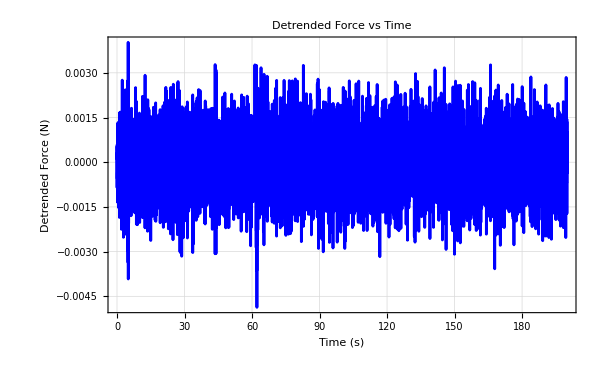

```mathematica
"■"; ListLinePlot[{time1[[1;;n-1]],force1Δ}ᵀ,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Detrended Force (N)"},LabelStyle->{12,Black},PlotLabel->"Detrended Force vs Time",ImageSize->600]
```

Note that in detrending via this differencing approach our mean is now 0 (or very close to 0):

```mathematica
"■";  Mean[force1Δ]
```

1.60115×10^-7

We should also determine the standard deviation:

```mathematica
"■";  force1SD=StandardDeviation[force1Δ]
```

0.000903811

#### Force Probability Density and Distribution Functions

Lets determine the non-parametric probability density function of the force. If we suspect that a signal is dominated by measurement noise then it is common to start by determining the probability density over a range of amplitudes ±4 SD about the mean:

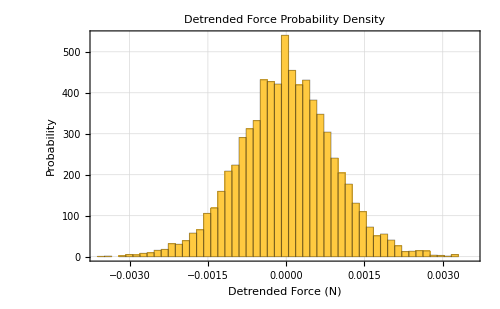

```mathematica
"■";  Histogram[force1Δ,{-4 force1SD,4 force1SD,0.15force1SD},"PDF",PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density",ImageSize->500]
```

Mathematica provides a wide range of alternative methods to compute probability density functions from data. Another algorithm generates smoothed probability densities:

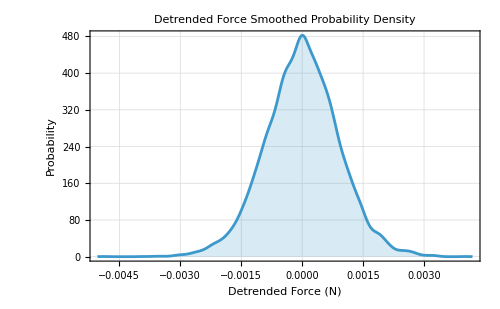

```mathematica
"■";  SmoothHistogram[force1Δ,Automatic,"PDF",Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Smoothed Probability Density",ImageSize->500]
```

A benefit of the SmoothHistogram[] function is that it eliminates the need to select a bin width as it does this automatically. This looks similar in shape to a Gaussian probability density function (i.e., a “bell shape”). 
We would like to find the best fit Gaussian probability density function to the force data. The Gaussian probability density function is a nonlinear function having 2 parameters: the mean, μ, and standard deviation, σ .

pdf(x)=1/(σ √(2π))e^(-1/2((x-μ)/σ)^2)

Normally we would have to use a nonlinear minimization algorithm to find the best fit parameters, μ and σ,  iteratively. However this is not required as the computed mean and standard deviation are already the least squares best fit parameters!
So we can now plot the best fit Gaussian probability density together with the measured (non-parametric) probability density function:

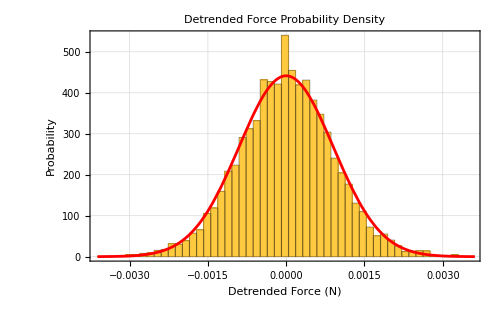

```mathematica
"■"; Show[
Histogram[force1Δ,{-4 force1SD,4 force1SD,0.15force1SD},"PDF",PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density",ImageSize->500],
Plot[PDF[NormalDistribution[0,force1SD],x],{x,-4 force1SD,4 force1SD},PlotStyle->Red]]
```

and for the smoothed probability density function estimate:

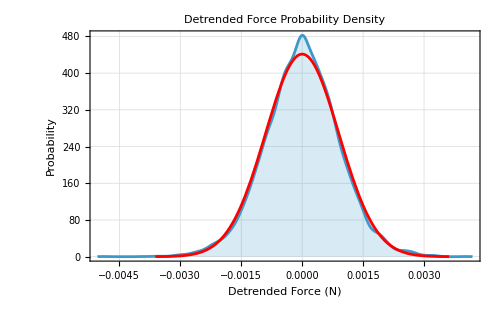

```mathematica
"■"; Show[
SmoothHistogram[force1Δ,Automatic,"PDF",Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density",ImageSize->500],
Plot[PDF[NormalDistribution[0,force1SD],x],{x,-4 force1SD,4 force1SD},PlotStyle->Red]]
```

It certainly looks like the force sensor noise is Gaussian.

Lets also look at the force probability distribution function:

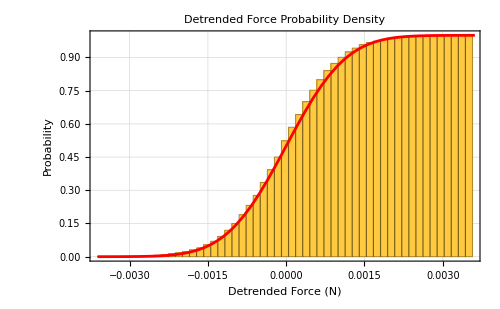

```mathematica
"■"; Show[
Histogram[force1Δ,{-4 force1SD,4 force1SD,0.15force1SD},"CDF",PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density",ImageSize->500],
Plot[CDF[NormalDistribution[0,force1SD],x],{x,-4 force1SD,4 force1SD},PlotStyle->Red]]
```

and for the smoothed probability density function estimate:

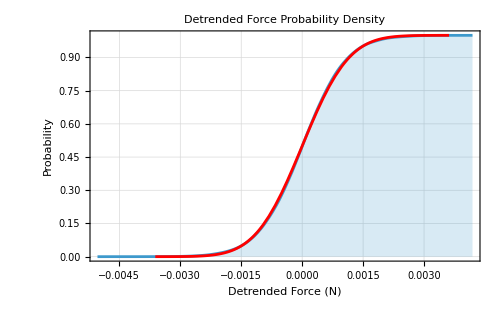

```mathematica
"■"; Show[
SmoothHistogram[force1Δ,Automatic,"CDF",Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density",ImageSize->500],
Plot[CDF[NormalDistribution[0,force1SD],x],{x,-4 force1SD,4 force1SD},PlotStyle->Red]]
```

These are so close that it is hard to distinguish the Gaussian probability distribution function from the non-parametric distribution function.

It is tempting to conclude that the force signal is Gaussian white noise. However at this point while the signal definitely looks Gaussian we do not know that it is also white (i.e., each sample is statistically independent of each other). 

It is useful to consider two main properties of any signal:
1. the sequential structure of the signal as measured by its power spectrum in the frequency domain or the auto-correlation function in the time (or lag) domain,
2. the amplitude structure of the signal as measured by its probability density function or its integral, the probability distribution function.

When we say that a signal is Gaussian white noise we are referring to two major properties of the signal:
1. that the sequential structure is white: meaning that its power spectrum is flat (i.e., all frequencies equally present), and
2. that the amplitude structure is Gaussian: meaning that its probability density appears Gaussian.

In subsequent notes we will consider how to estimate both of these properties from measured signals.

#### Determination of Force Resolution

We can ask if it is possible to determine the resolution of the force measurement from the data. Lets give this a try on the detrended force data (we could have used the original force measurements also, it should make no difference). We start by plotting the detrended force measurements as points and zoom in around 0.0:

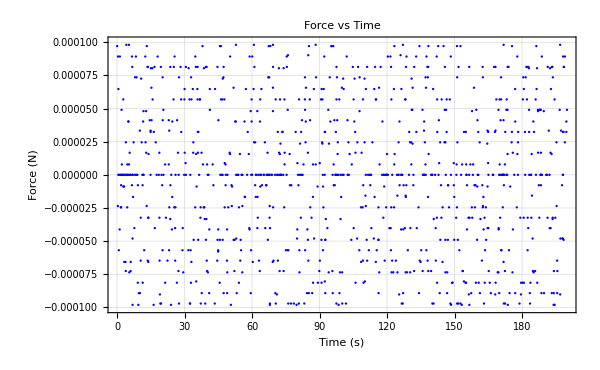

```mathematica
"■"; ListPlot[{time1[[1;;n-1]],force1Δ}ᵀ,PlotRange->{All,{-0.0001,0.0001}},PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Force (N)"},LabelStyle->{12,Black},PlotLabel->"Force vs Time",ImageSize->600]
```

Lets replot in μN

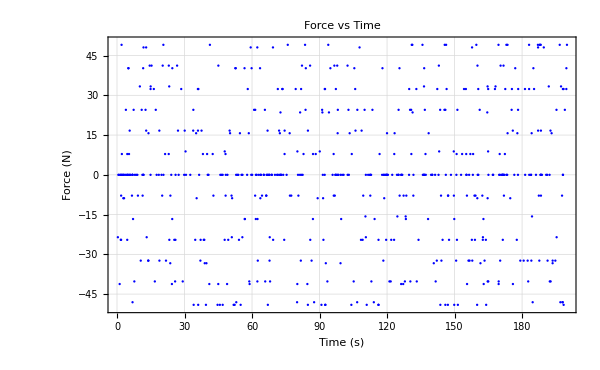

```mathematica
"■"; ListPlot[{time1[[1;;n-1]],10^6 force1Δ}ᵀ,PlotRange->{All,{-50,50}},PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Force (N)"},LabelStyle->{12,Black},PlotLabel->"Force vs Time",ImageSize->600]
```

It certainly looks as though we have distinct rows of measurements separated by some increment that looks to be around 10 μN. There is also some small fluctuations that can be seen in the values in each row.

These rows of data points correspond to the smallest values resolvable by the force sensor ADC. 
We want an algorithm to find the minimum force difference (or increment).

We can use the DeleteDuplicates[] function to find all the distinctly different forces (we will just plot a 10 of them):

```mathematica
"■"; for1=DeleteDuplicates[force1Δ,Abs[#1-#2]<=0.0000001&];
```

Note that we specified that any force that were within 0.0000001 N (i.e. 100 nN) are treated as being equal.

We can now sort these:

```mathematica
"■"; for1Sorted=Sort[for1];
```

and determine the differences between these sorted forces:

```mathematica
"■"; Differences[for1Sorted];
```

The minimum force increment in μN will then be given by:

```mathematica
"■"; Δfor1=10^6 Min[Differences[for1Sorted]]
```

0.981

So we have just experimentally determined the minimum force increment (otherwise known as the force resolution) as 0.981 N = 0.981 μN.

```mathematica
UnitConvert[Quantity[0.981,"MicroNewtons"],"MilliGramsForce"]
```

0.100034 mgf

This is as expected as the TinkerForge Load Cell Bricklet returns integer values. We had specified that 1 kg mass on the force sensor during calibration would correspond to 10,000,000. This means that if the Load Cell returns 1 (the minimum absolute value) then this corresponds to 0.1 mg (force) = 0.981 μN.
However this is an artificial resolution as it was set by our selection of 10,000,000 when we calibrated the force sensor. The actual resolution is the 10 μN dominant row separation seen in the plot above.

#### Analysis of the Temperature Signal

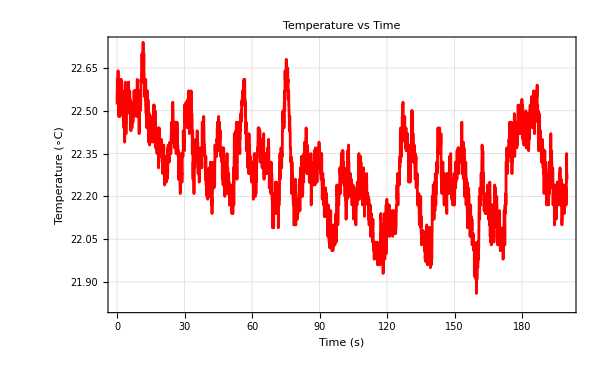

```mathematica
"■"; ListLinePlot[{time1,temperature1}ᵀ,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Temperature (∘C)"},LabelStyle->{12,Black},PlotLabel->"Temperature vs Time",ImageSize->600]
```

We can see a small drift in temperature (your temperature signal may or may not show this). 
We also see what appears to be small random step changes in temperature. This is caused by the limited resolution (dynamic range) of the Thermocouple Bricklet analog to digital converter (ADC). This ADC “bit quantization” is easier to see when we detrend the data:

```mathematica
"■"; temperature1Δ=Differences[temperature1];
```

Note that the length of the force1Δ signal will be n-1. Lets plot the linearly detrended signal:

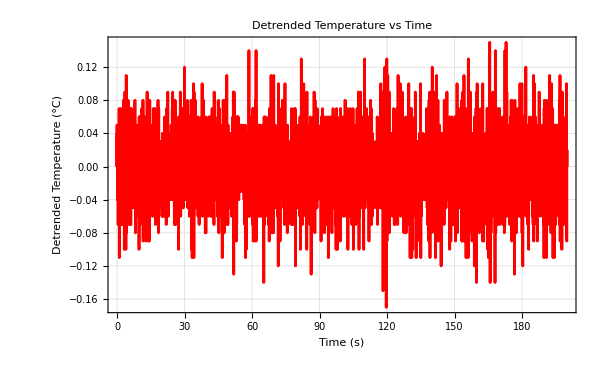

```mathematica
"■"; ListLinePlot[{time1[[1;;n-1]],temperature1Δ}ᵀ,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Detrended Temperature (°C)"},LabelStyle->{12,Black},PlotLabel->"Detrended Temperature vs Time",ImageSize->600]
```

Note that in detrending via this differencing approach our mean is now 0 (or very close to 0):

```mathematica
"■";  Mean[temperature1Δ]
```

-0.0000240024

We should also determine the standard deviation:

```mathematica
"■";  temperature1SD=StandardDeviation[temperature1Δ]
```

0.0223669

#### Determination of Temperature Resolution

We can ask if it is possible to determine the resolution of the temperature measurements from the data. Lets give this a try on the detrended temperature data (we could have used the original temperature measurements also, it should make no difference). We start by plotting the detrended temperature measurements as points and zoom in around 0.0:

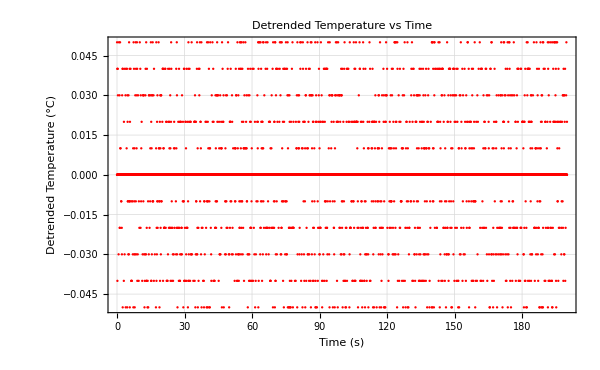

```mathematica
"■"; ListPlot[{time1[[1;;n-1]],temperature1Δ}ᵀ,PlotRange->{All,{-0.05,0.05}},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Detrended Temperature (°C)"},LabelStyle->{12,Black},PlotLabel->"Detrended Temperature vs Time",ImageSize->600]
```

It is clear that the minimum separation between these rows is 0.01 °C

These rows of data points correspond to the smallest values resolvable by the thermocouple sensor ADC. 
We want an algorithm to find the minimum temperature difference (or increment).

We can use the DeleteDuplicates[] function to find all the distinctly different temperature (we will just plot a 10 of them):

```mathematica
"■"; temp1=DeleteDuplicates[temperature1Δ,Abs[#1-#2]<=0.00001&];
```

Note that we specified that any temperature that were within 0.00001 °C (i.e. 100 μ°C) are treated as being equal.

We can now sort these:

```mathematica
"■"; temp1Sorted=Sort[temp1];
```

and determine the differences between these sorted forces:

```mathematica
"■"; Differences[temp1Sorted];
```

The minimum temperature increment in °C will then be given by:

```mathematica
"■"; Δtemp1=Min[Differences[temp1Sorted]]
```

0.01

So we have just experimentally determined the minimum temperature increment (otherwise known as the temperature resolution) as 0.01 ∘C. This corresponds to the published spec of the thermocouple chip used in the TinkerForge temperature bricklet.

#### Temperature Probability Density

Lets look at the detrended temperature probability density:

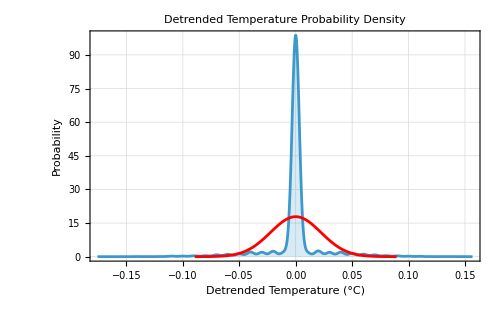

```mathematica
"■"; Show[
SmoothHistogram[temperature1Δ,Automatic,"PDF",Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"Detrended Temperature (°C)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Temperature Probability Density",ImageSize->500],
Plot[PDF[NormalDistribution[0,temperature1SD],x],{x,-4 temperature1SD,4 temperature1SD},PlotStyle->Red]]
```

There is no reason to expect that the temperature fluctuations should be Gaussian. The measurements will be dominated by temperature changes due to air currents. Over a long time period these environmental temperature changes may be Gaussian sitting on some periodic temperature changes such as day vs night transitions. To find out the true temperature noise of these thermocouple sensors we would need to put them in a temperature controlled environment (preferably with temperature control better than to within 0.01 °C).

#### Experiment 2: Measure Force (with 1 kg load) and Temperature for 200 s

As in Experiment 1 we set TinkerForge Load Cell Bricklet to have an internal sampling rate of 80 Hz. To avoid the possibility of reading the same sample more than once we need to read the Load Cell Bricklet at less than this value. So in the following experiment we will sample it and the thermocouple at 50 Hz (i.e., once every 20 ms). We will collect 10,000 samples per signal. 10,000 samples x 0.02 s = 200 s experimental duration. We will use polling as outlined above. You should avoid bumping the setup while running the experiment.
Place the 1 kg mass on the force sensor and wait for 10 s (for any load transient to decay) and then start the experiment. The 1 kg mass sitting on the force sensor will pick up small table vibrations. The code below gives you 5 s to move away from the table after you start the experiment.

```mathematica
"■"; 
Pause[5]; (* give time to move away from table/bench holding the setup *)
n=10000;
time2=Table[0,n];
temperature2=Table[0,n]; (* in oC *)
force2=Table[0,n]; (* in Newtons *)
δt=0.02; (* desired inter-sample interval in s *)
t0=AbsoluteTime[];
Do[
While[(AbsoluteTime[]-t0)< δt(i-1)];
time2[[i]]= AbsoluteTime[]-t0; 
temperature2[[i]]=tc@GetTemperature[]/100.0;
force2[[i]]=9.81 (lc@GetWeight[])/10000000;
If[Mod[i,1000]==0, (* print out every 1000th sample index *)
Print[i]],
{i,n}]
```

1000

2000

3000

4000

5000

6000

7000

8000

9000

10000

#### Store Data

By default Mathematica does not store large amounts of data. We can force it store our force and temperature signals using:

```mathematica
"■";  PersistentSymbol["1kgMassForceTemperatureData"]={time2,force2,temperature2};
```

#### Force Signal Amplitude Analysis

Lets plot the force signal:

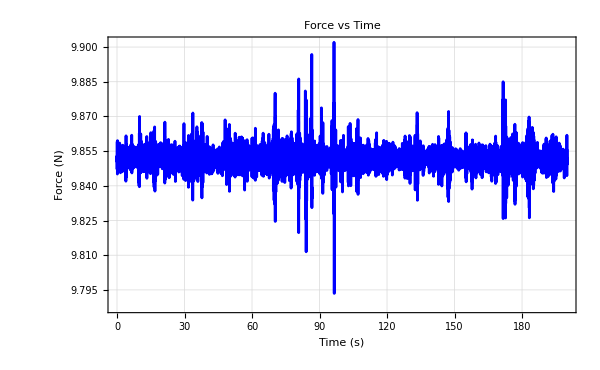

```mathematica
"■"; ListLinePlot[{time2,force2}ᵀ,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Force (N)"},LabelStyle->{12,Black},PlotLabel->"Force vs Time",ImageSize->600]
```

If you see large spikes in this plot then it was probably because the force sensor picked up some movement in the room (e.g., table vibration cause by a bump). It is best to rerun the experiment if this is evident.
We can see that there is a small drift in the force signal (your data may or may not show this).

We take successive differences between adjacent data points:

```mathematica
"■"; force2Δ=Differences[force2];
```

Note that the length of the forceΔ signal will be n-1. Lets plot the linearly detrended signal:

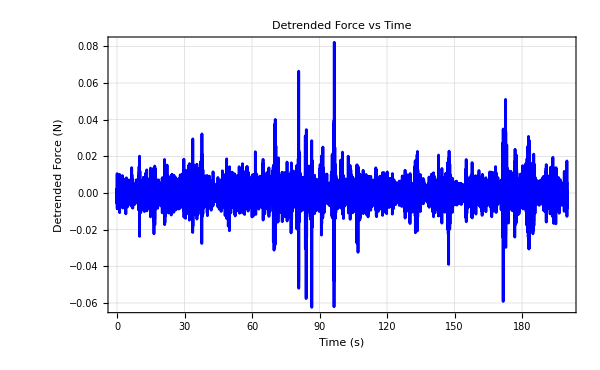

```mathematica
"■"; ListLinePlot[{time2[[1;;n-1]],force2Δ}ᵀ,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Time (s)", "Detrended Force (N)"},LabelStyle->{12,Black},PlotLabel->"Detrended Force vs Time",ImageSize->600]
```

Note that in detrending via this differencing approach our mean is now 0 (or very close to 0):

```mathematica
"■";  Mean[force2Δ]
```

5.76886×10^-8

We should also determine the standard deviation:

```mathematica
"■";  force2SD=StandardDeviation[force2Δ]
```

0.00585872

#### Force Probability Density Functions

Lets look at the probability density function of the measured detrended force data:

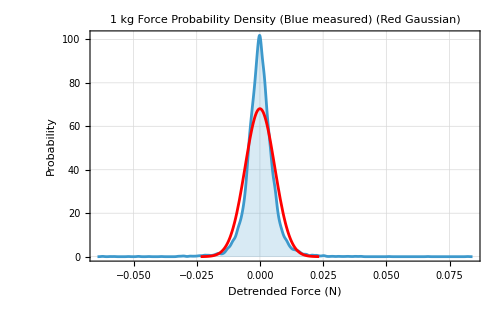

```mathematica
"■"; Show[
SmoothHistogram[force2Δ,Automatic,"PDF",Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"1 kg Force Probability Density (Blue measured) (Red Gaussian)",ImageSize->500],
Plot[PDF[NormalDistribution[0,force2SD],x],{x,-4 force2SD,4 force2SD},PlotStyle->Red]]
```

The data look highly Gaussian. A common assumption made is to assume that the noise variation will increase with amplitude. This is not necessarily the case. Lets compare the force probability densities of the detrended 0 load and 1 kg mass load experiments:

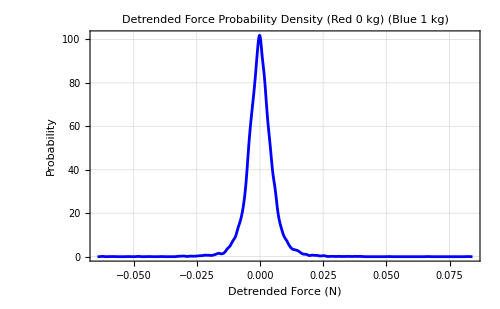

```mathematica
"■"; 
SmoothHistogram[{force1Δ,force2Δ},Automatic,"PDF",PlotStyle->{Red,Blue},PlotTheme->"Detailed",FrameLabel->{"Detrended Force (N)","Probability"},LabelStyle->{12,Black},PlotLabel->"Detrended Force Probability Density (Red 0 kg) (Blue 1 kg)",ImageSize->500]
```

As you can see this particular force sensor noise is not dependent upon force mean amplitude (at least not over this range).
Note that the assumption that measurement noise levels are independent on the amplitude of a signal is implicit when you use common least squares fitting of linear or nonlinear functions to data. If you have sensors where their noise levels change with amplitude then weighted least squares should be used.